```mathematica
a=Import["G:\\calc-online\\gpd\\k-result\\diagram-l-q-n.wdx"];
```

```mathematica
f1=Query[1,1]@a;
g1=Query[1,2]@a;
f2=Query[2,1]@a;
g2=Query[2,2]@a;
nf1=f1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Q^2->1,q3->0.97710345,Λ->1};
ng1=g1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Q^2->1,q3->0.97710345,Λ->1};
nf2=f2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Q^2->1,q3->0.97710345,Λ->1};
ng2=g2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Q^2->1,q3->0.97710345,Λ->1};
```

```mathematica
b1=f1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Q^2->1,q3->0.90494455,Λ->1};
b2=g1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Q^2->1,q3->0.90494455,Λ->1};
b3=f2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Q^2->1,q3->0.90494455,Λ->1};
b4=g2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Q^2->1,q3->0.90494455,Λ->1};
```

```mathematica
NIntegrate[nf1,{k3,0,∞},{θ,0,2π},{y,-0.1,0.1},WorkingPrecision->10]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.87351002111876262472670074019410489369402683123906582577388×10^-11 and 1.22107668360918559339130806677908757624681777272469528688736×10^-9 for the integral and error estimates.

6.873510021×10^-11

```mathematica
NIntegrate[ng1,{k3,0,∞},{θ,0,2π},{y,-0.1,0.1},WorkingPrecision->10]
```

1.228492009

```mathematica
Simplify[nf1]
```

-((0.130927 k3 y (-9.05555-214.377 y+71.112 y^2+37572.9 y^3+255101. y^4-1.0784×10^6 y^5-1.69327×10^7 y^6-5.40009×10^7 y^7-2.31489×10^7 y^8+4.88034×10^7 y^9-1.42355×10^7 y^10+1.13393×10^6 y^11-6.07607×10^-11 y^12+3.71752×10^-12 y^13+k3^12 (-7.26077×10^-16-2.30177×10^-14 y-9.45413×10^-14 y^2+6.30275×10^-13 y^3)+k3^10 y (-9.42287×10^-14-1.27273×10^-12 y-1.73009×10^-12 y^2+1.56242×10^-11 y^3-1.19447×10^-12 y^4)+k3^8 (-1.41988×10^-14-4.54747×10^-13 y-4.84808×10^-12 y^2-2.18279×10^-11 y^3-9.09759×10^-12 y^4+1.88701×10^-10 y^5-1.20982×10^-11 y^6-7.88076×10^-13 y^7)+k3^6 (-7.82289-78.2289 y+1564.58 y^2+15645.8 y^3-78228.9 y^4-782289. y^5+1.86092×10^-9 y^6-1.71609×10^-10 y^7-3.23252×10^-11 y^8+2.71905×10^-12 y^9)+k3^4 (-24.7058-359.089 y+3847.41 y^2+72083.5 y^3-28307.4 y^4-3.64401×10^6 y^5-1.09375×10^7 y^6+2.656×10^6 y^7-3.09818×10^-9 y^8+4.18249×10^-11 y^9+2.98385×10^-11 y^10-1.37038×10^-12 y^11)+k3^2 (-25.9385-495.259 y+2412.8 y^2+95143.8 y^3+298099. y^4-4.1713×10^6 y^5-2.825×10^7 y^6-3.90192×10^7 y^7+2.50571×10^7 y^8-3.00585×10^6 y^9+2.14051×10^-9 y^10-9.03848×10^-11 y^11-2.85495×10^-13 y^12)+k3 (-43.8801-990.81 y+198.38 y^2+166647. y^3+1.24202×10^6 y^4-3.5813×10^6 y^5-7.88377×10^7 y^6-3.19925×10^8 y^7-3.46492×10^8 y^8+2.38959×10^8 y^9-2.91381×10^7 y^10+3.22218×10^-9 y^11-1.61918×10^-10 y^12+k3^10 (-1.8394×10^-14-3.1302×10^-13 y-1.56793×10^-12 y^2-7.97711×10^-13 y^3+1.97359×10^-11 y^4)+k3^8 (1.80713×10^-14-1.91039×10^-13 y-8.42637×10^-12 y^2-5.13843×10^-11 y^3-9.16481×10^-12 y^4+3.36093×10^-10 y^5-1.83846×10^-11 y^6)+k3^6 (-16.0124-3.86535×10^-12 y+3202.48 y^2-2.47383×10^-10 y^3-160124. y^4+2.52956×10^-10 y^5+3.85457×10^-9 y^6+2.88576×10^-11 y^7-3.42202×10^-11 y^8)+k3^4 (-73.5008-687.939 y+12461.4 y^2+137588. y^3-287255. y^4-6.87939×10^6 y^5-2.23877×10^7 y^6+3.22485×10^-8 y^7-2.9186×10^-9 y^8-4.66887×10^-10 y^9+3.36674×10^-11 y^10)+k3^2 (-101.373-1667.34 y+10268. y^2+313132. y^3+992715. y^4-1.26062×10^7 y^5-1.01091×10^8 y^6-2.03361×10^8 y^7+5.12884×10^7 y^8-3.5746×10^-8 y^9+2.85891×10^-9 y^10+5.56754×10^-12 y^11)) Cos[θ]+k3^2 (-75.4643-1805.1 y-716.573 y^2+298289. y^3+2.3129×10^6 y^4-5.48014×10^6 y^5-1.39226×10^8 y^6-6.32256×10^8 y^7-9.43411×10^8 y^8+2.47565×10^8 y^9-3.06971×10^-8 y^10+3.91248×10^-9 y^11+k3^8 (-1.16172×10^-14-4.46618×10^-13 y-5.36974×10^-12 y^2-2.11229×10^-11 y^3+1.70466×10^-11 y^4+2.17474×10^-10 y^5)+k3^6 (-3.87241×10^-13-8.74649×10^-12 y-6.5263×10^-11 y^2-1.75797×10^-10 y^3-1.66545×10^-10 y^4-3.94294×10^-10 y^5+2.13555×10^-9 y^6-1.71528×10^-11 y^7)+k3^4 (-46.9373-469.373 y+9387.46 y^2+93874.6 y^3-469373. y^4-4.69373×10^6 y^5+5.17759×10^-9 y^6+2.44252×10^-8 y^7+1.39805×10^-9 y^8-2.59126×10^-10 y^9)+k3^2 (-121.229-2108.55 y+13149. y^2+400365. y^3+1.00708×10^6 y^4-1.68167×10^7 y^5-1.10969×10^8 y^6-2.13439×10^8 y^7+1.61929×10^-7 y^8-2.60673×10^-8 y^9-1.74318×10^-11 y^10)) Cos[θ]^2+k3^3 (-55.578-1476.45 y-2417.82 y^2+245243. y^3+2.08312×10^6 y^4-4.75524×10^6 y^5-1.21777×10^8 y^6-5.00461×10^8 y^7-6.77871×10^8 y^8+4.16838×10^-8 y^9+1.07858×10^-8 y^10+k3^6 (5.2923×10^-14-5.03414×10^-13 y-1.03264×10^-11 y^2-1.1896×10^-11 y^3-1.06952×10^-10 y^4+2.14984×10^-10 y^5+9.49012×10^-10 y^6)+k3^4 (-1.75549×10^-13-7.37307×10^-12 y-1.22265×10^-10 y^2-1.10501×10^-9 y^3-4.80072×10^-9 y^4-3.93363×10^-9 y^5-3.04315×10^-9 y^6+3.45347×10^-9 y^7+4.73345×10^-10 y^8)+k3^2 (-45.8626-917.252 y+4586.26 y^2+183450. y^3+458626. y^4-9.17252×10^6 y^5-4.58626×10^7 y^6+2.74296×10^-8 y^7+6.2791×10^-8 y^8-2.01201×10^-10 y^9)) Cos[θ]^3+k3^4 (-14.9375-448.125 y-1493.75 y^2+74687.5 y^3+746875. y^4-1.49375×10^6 y^5-4.48125×10^7 y^6-1.49375×10^8 y^7+2.49468×10^-7 y^8-4.3143×10^-8 y^9+k3^4 (1.03264×10^-14+1.13591×10^-12 y-6.19586×10^-12 y^2-2.97401×10^-10 y^3-1.50155×10^-9 y^4-1.74429×10^-9 y^5+6.50896×10^-10 y^6+1.17593×10^-9 y^7)+k3^2 (-5.42138×10^-14-1.94653×10^-12 y-3.46968×10^-12 y^2-1.16317×10^-10 y^3-4.50464×10^-9 y^4-2.35172×10^-8 y^5-1.0246×10^-8 y^6-3.46874×10^-8 y^7+9.7163×10^-10 y^8)) Cos[θ]^4+k3^5 (-1.60544×10^-14+(-1.16221×10^-12+5.16322×10^-13 k3^2) y+(-2.55476×10^-11+2.30073×10^-11 k3^2) y^2+(-5.41931×10^-10+1.57292×10^-10 k3^2) y^3+(-5.93877×10^-9-8.24793×10^-10 k3^2) y^4+(-2.4913×10^-8-7.1905×10^-9 k3^2) y^5+(-5.03335×10^-8-1.05155×10^-8 k3^2) y^6+(-8.44249×10^-8+5.87966×10^-10 k3^2) y^7+1.69188×10^-9 y^8) Cos[θ]^5+k3^6 y (1.2908×10^-13+1.2908×10^-12 y-6.60892×10^-11 y^2-9.25248×10^-10 y^3-2.64357×10^-9 y^4) Cos[θ]^6))/((0.998219+1. k3^2-0.130986 y-1.13172 y^2+k3 (0.977103+9.77103 y) Cos[θ])^2 (0.507754+1. k3^2+4.77366 y-1.13172 y^2+k3 (0.977103+9.77103 y) Cos[θ]) (1.48868+1. k3^2+4.77366 y-1.13172 y^2+k3 (0.977103+9.77103 y) Cos[θ])^3 (0.998219+1. k3^2+9.6783 y-1.13172 y^2+k3 (0.977103+9.77103 y) Cos[θ])^2))

```mathematica
Cancel[%10]
```

-((0.130927 k3 y (-9.05555-25.9385 k3^2-24.7058 k3^4-7.82289 k3^6-1.41988×10^-14 k3^8-7.26077×10^-16 k3^12-214.377 y-495.259 k3^2 y-359.089 k3^4 y-78.2289 k3^6 y-4.54747×10^-13 k3^8 y-9.42287×10^-14 k3^10 y-2.30177×10^-14 k3^12 y+71.112 y^2+2412.8 k3^2 y^2+3847.41 k3^4 y^2+1564.58 k3^6 y^2-4.84808×10^-12 k3^8 y^2-1.27273×10^-12 k3^10 y^2-9.45413×10^-14 k3^12 y^2+37572.9 y^3+95143.8 k3^2 y^3+72083.5 k3^4 y^3+15645.8 k3^6 y^3-2.18279×10^-11 k3^8 y^3-1.73009×10^-12 k3^10 y^3+6.30275×10^-13 k3^12 y^3+255101. y^4+298099. k3^2 y^4-28307.4 k3^4 y^4-78228.9 k3^6 y^4-9.09759×10^-12 k3^8 y^4+1.56242×10^-11 k3^10 y^4-1.0784×10^6 y^5-4.1713×10^6 k3^2 y^5-3.64401×10^6 k3^4 y^5-782289. k3^6 y^5+1.88701×10^-10 k3^8 y^5-1.19447×10^-12 k3^10 y^5-1.69327×10^7 y^6-2.825×10^7 k3^2 y^6-1.09375×10^7 k3^4 y^6+1.86092×10^-9 k3^6 y^6-1.20982×10^-11 k3^8 y^6-5.40009×10^7 y^7-3.90192×10^7 k3^2 y^7+2.656×10^6 k3^4 y^7-1.71609×10^-10 k3^6 y^7-7.88076×10^-13 k3^8 y^7-2.31489×10^7 y^8+2.50571×10^7 k3^2 y^8-3.09818×10^-9 k3^4 y^8-3.23252×10^-11 k3^6 y^8+4.88034×10^7 y^9-3.00585×10^6 k3^2 y^9+4.18249×10^-11 k3^4 y^9+2.71905×10^-12 k3^6 y^9-1.42355×10^7 y^10+2.14051×10^-9 k3^2 y^10+2.98385×10^-11 k3^4 y^10+1.13393×10^6 y^11-9.03848×10^-11 k3^2 y^11-1.37038×10^-12 k3^4 y^11-6.07607×10^-11 y^12-2.85495×10^-13 k3^2 y^12+3.71752×10^-12 y^13-43.8801 k3 Cos[θ]-101.373 k3^3 Cos[θ]-73.5008 k3^5 Cos[θ]-16.0124 k3^7 Cos[θ]+1.80713×10^-14 k3^9 Cos[θ]-1.8394×10^-14 k3^11 Cos[θ]-990.81 k3 y Cos[θ]-1667.34 k3^3 y Cos[θ]-687.939 k3^5 y Cos[θ]-3.86535×10^-12 k3^7 y Cos[θ]-1.91039×10^-13 k3^9 y Cos[θ]-3.1302×10^-13 k3^11 y Cos[θ]+198.38 k3 y^2 Cos[θ]+10268. k3^3 y^2 Cos[θ]+12461.4 k3^5 y^2 Cos[θ]+3202.48 k3^7 y^2 Cos[θ]-8.42637×10^-12 k3^9 y^2 Cos[θ]-1.56793×10^-12 k3^11 y^2 Cos[θ]+166647. k3 y^3 Cos[θ]+313132. k3^3 y^3 Cos[θ]+137588. k3^5 y^3 Cos[θ]-2.47383×10^-10 k3^7 y^3 Cos[θ]-5.13843×10^-11 k3^9 y^3 Cos[θ]-7.97711×10^-13 k3^11 y^3 Cos[θ]+1.24202×10^6 k3 y^4 Cos[θ]+992715. k3^3 y^4 Cos[θ]-287255. k3^5 y^4 Cos[θ]-160124. k3^7 y^4 Cos[θ]-9.16481×10^-12 k3^9 y^4 Cos[θ]+1.97359×10^-11 k3^11 y^4 Cos[θ]-3.5813×10^6 k3 y^5 Cos[θ]-1.26062×10^7 k3^3 y^5 Cos[θ]-6.87939×10^6 k3^5 y^5 Cos[θ]+2.52956×10^-10 k3^7 y^5 Cos[θ]+3.36093×10^-10 k3^9 y^5 Cos[θ]-7.88377×10^7 k3 y^6 Cos[θ]-1.01091×10^8 k3^3 y^6 Cos[θ]-2.23877×10^7 k3^5 y^6 Cos[θ]+3.85457×10^-9 k3^7 y^6 Cos[θ]-1.83846×10^-11 k3^9 y^6 Cos[θ]-3.19925×10^8 k3 y^7 Cos[θ]-2.03361×10^8 k3^3 y^7 Cos[θ]+3.22485×10^-8 k3^5 y^7 Cos[θ]+2.88576×10^-11 k3^7 y^7 Cos[θ]-3.46492×10^8 k3 y^8 Cos[θ]+5.12884×10^7 k3^3 y^8 Cos[θ]-2.9186×10^-9 k3^5 y^8 Cos[θ]-3.42202×10^-11 k3^7 y^8 Cos[θ]+2.38959×10^8 k3 y^9 Cos[θ]-3.5746×10^-8 k3^3 y^9 Cos[θ]-4.66887×10^-10 k3^5 y^9 Cos[θ]-2.91381×10^7 k3 y^10 Cos[θ]+2.85891×10^-9 k3^3 y^10 Cos[θ]+3.36674×10^-11 k3^5 y^10 Cos[θ]+3.22218×10^-9 k3 y^11 Cos[θ]+5.56754×10^-12 k3^3 y^11 Cos[θ]-1.61918×10^-10 k3 y^12 Cos[θ]-75.4643 k3^2 Cos[θ]^2-121.229 k3^4 Cos[θ]^2-46.9373 k3^6 Cos[θ]^2-3.87241×10^-13 k3^8 Cos[θ]^2-1.16172×10^-14 k3^10 Cos[θ]^2-1805.1 k3^2 y Cos[θ]^2-2108.55 k3^4 y Cos[θ]^2-469.373 k3^6 y Cos[θ]^2-8.74649×10^-12 k3^8 y Cos[θ]^2-4.46618×10^-13 k3^10 y Cos[θ]^2-716.573 k3^2 y^2 Cos[θ]^2+13149. k3^4 y^2 Cos[θ]^2+9387.46 k3^6 y^2 Cos[θ]^2-6.5263×10^-11 k3^8 y^2 Cos[θ]^2-5.36974×10^-12 k3^10 y^2 Cos[θ]^2+298289. k3^2 y^3 Cos[θ]^2+400365. k3^4 y^3 Cos[θ]^2+93874.6 k3^6 y^3 Cos[θ]^2-1.75797×10^-10 k3^8 y^3 Cos[θ]^2-2.11229×10^-11 k3^10 y^3 Cos[θ]^2+2.3129×10^6 k3^2 y^4 Cos[θ]^2+1.00708×10^6 k3^4 y^4 Cos[θ]^2-469373. k3^6 y^4 Cos[θ]^2-1.66545×10^-10 k3^8 y^4 Cos[θ]^2+1.70466×10^-11 k3^10 y^4 Cos[θ]^2-5.48014×10^6 k3^2 y^5 Cos[θ]^2-1.68167×10^7 k3^4 y^5 Cos[θ]^2-4.69373×10^6 k3^6 y^5 Cos[θ]^2-3.94294×10^-10 k3^8 y^5 Cos[θ]^2+2.17474×10^-10 k3^10 y^5 Cos[θ]^2-1.39226×10^8 k3^2 y^6 Cos[θ]^2-1.10969×10^8 k3^4 y^6 Cos[θ]^2+5.17759×10^-9 k3^6 y^6 Cos[θ]^2+2.13555×10^-9 k3^8 y^6 Cos[θ]^2-6.32256×10^8 k3^2 y^7 Cos[θ]^2-2.13439×10^8 k3^4 y^7 Cos[θ]^2+2.44252×10^-8 k3^6 y^7 Cos[θ]^2-1.71528×10^-11 k3^8 y^7 Cos[θ]^2-9.43411×10^8 k3^2 y^8 Cos[θ]^2+1.61929×10^-7 k3^4 y^8 Cos[θ]^2+1.39805×10^-9 k3^6 y^8 Cos[θ]^2+2.47565×10^8 k3^2 y^9 Cos[θ]^2-2.60673×10^-8 k3^4 y^9 Cos[θ]^2-2.59126×10^-10 k3^6 y^9 Cos[θ]^2-3.06971×10^-8 k3^2 y^10 Cos[θ]^2-1.74318×10^-11 k3^4 y^10 Cos[θ]^2+3.91248×10^-9 k3^2 y^11 Cos[θ]^2-55.578 k3^3 Cos[θ]^3-45.8626 k3^5 Cos[θ]^3-1.75549×10^-13 k3^7 Cos[θ]^3+5.2923×10^-14 k3^9 Cos[θ]^3-1476.45 k3^3 y Cos[θ]^3-917.252 k3^5 y Cos[θ]^3-7.37307×10^-12 k3^7 y Cos[θ]^3-5.03414×10^-13 k3^9 y Cos[θ]^3-2417.82 k3^3 y^2 Cos[θ]^3+4586.26 k3^5 y^2 Cos[θ]^3-1.22265×10^-10 k3^7 y^2 Cos[θ]^3-1.03264×10^-11 k3^9 y^2 Cos[θ]^3+245243. k3^3 y^3 Cos[θ]^3+183450. k3^5 y^3 Cos[θ]^3-1.10501×10^-9 k3^7 y^3 Cos[θ]^3-1.1896×10^-11 k3^9 y^3 Cos[θ]^3+2.08312×10^6 k3^3 y^4 Cos[θ]^3+458626. k3^5 y^4 Cos[θ]^3-4.80072×10^-9 k3^7 y^4 Cos[θ]^3-1.06952×10^-10 k3^9 y^4 Cos[θ]^3-4.75524×10^6 k3^3 y^5 Cos[θ]^3-9.17252×10^6 k3^5 y^5 Cos[θ]^3-3.93363×10^-9 k3^7 y^5 Cos[θ]^3+2.14984×10^-10 k3^9 y^5 Cos[θ]^3-1.21777×10^8 k3^3 y^6 Cos[θ]^3-4.58626×10^7 k3^5 y^6 Cos[θ]^3-3.04315×10^-9 k3^7 y^6 Cos[θ]^3+9.49012×10^-10 k3^9 y^6 Cos[θ]^3-5.00461×10^8 k3^3 y^7 Cos[θ]^3+2.74296×10^-8 k3^5 y^7 Cos[θ]^3+3.45347×10^-9 k3^7 y^7 Cos[θ]^3-6.77871×10^8 k3^3 y^8 Cos[θ]^3+6.2791×10^-8 k3^5 y^8 Cos[θ]^3+4.73345×10^-10 k3^7 y^8 Cos[θ]^3+4.16838×10^-8 k3^3 y^9 Cos[θ]^3-2.01201×10^-10 k3^5 y^9 Cos[θ]^3+1.07858×10^-8 k3^3 y^10 Cos[θ]^3-14.9375 k3^4 Cos[θ]^4-5.42138×10^-14 k3^6 Cos[θ]^4+1.03264×10^-14 k3^8 Cos[θ]^4-448.125 k3^4 y Cos[θ]^4-1.94653×10^-12 k3^6 y Cos[θ]^4+1.13591×10^-12 k3^8 y Cos[θ]^4-1493.75 k3^4 y^2 Cos[θ]^4-3.46968×10^-12 k3^6 y^2 Cos[θ]^4-6.19586×10^-12 k3^8 y^2 Cos[θ]^4+74687.5 k3^4 y^3 Cos[θ]^4-1.16317×10^-10 k3^6 y^3 Cos[θ]^4-2.97401×10^-10 k3^8 y^3 Cos[θ]^4+746875. k3^4 y^4 Cos[θ]^4-4.50464×10^-9 k3^6 y^4 Cos[θ]^4-1.50155×10^-9 k3^8 y^4 Cos[θ]^4-1.49375×10^6 k3^4 y^5 Cos[θ]^4-2.35172×10^-8 k3^6 y^5 Cos[θ]^4-1.74429×10^-9 k3^8 y^5 Cos[θ]^4-4.48125×10^7 k3^4 y^6 Cos[θ]^4-1.0246×10^-8 k3^6 y^6 Cos[θ]^4+6.50896×10^-10 k3^8 y^6 Cos[θ]^4-1.49375×10^8 k3^4 y^7 Cos[θ]^4-3.46874×10^-8 k3^6 y^7 Cos[θ]^4+1.17593×10^-9 k3^8 y^7 Cos[θ]^4+2.49468×10^-7 k3^4 y^8 Cos[θ]^4+9.7163×10^-10 k3^6 y^8 Cos[θ]^4-4.3143×10^-8 k3^4 y^9 Cos[θ]^4-1.60544×10^-14 k3^5 Cos[θ]^5-1.16221×10^-12 k3^5 y Cos[θ]^5+5.16322×10^-13 k3^7 y Cos[θ]^5-2.55476×10^-11 k3^5 y^2 Cos[θ]^5+2.30073×10^-11 k3^7 y^2 Cos[θ]^5-5.41931×10^-10 k3^5 y^3 Cos[θ]^5+1.57292×10^-10 k3^7 y^3 Cos[θ]^5-5.93877×10^-9 k3^5 y^4 Cos[θ]^5-8.24793×10^-10 k3^7 y^4 Cos[θ]^5-2.4913×10^-8 k3^5 y^5 Cos[θ]^5-7.1905×10^-9 k3^7 y^5 Cos[θ]^5-5.03335×10^-8 k3^5 y^6 Cos[θ]^5-1.05155×10^-8 k3^7 y^6 Cos[θ]^5-8.44249×10^-8 k3^5 y^7 Cos[θ]^5+5.87966×10^-10 k3^7 y^7 Cos[θ]^5+1.69188×10^-9 k3^5 y^8 Cos[θ]^5+1.2908×10^-13 k3^6 y Cos[θ]^6+1.2908×10^-12 k3^6 y^2 Cos[θ]^6-6.60892×10^-11 k3^6 y^3 Cos[θ]^6-9.25248×10^-10 k3^6 y^4 Cos[θ]^6-2.64357×10^-9 k3^6 y^5 Cos[θ]^6))/((0.998219+1. k3^2-0.130986 y-1.13172 y^2+0.977103 k3 Cos[θ]+9.77103 k3 y Cos[θ])^2 (0.507754+1. k3^2+4.77366 y-1.13172 y^2+0.977103 k3 Cos[θ]+9.77103 k3 y Cos[θ]) (1.48868+1. k3^2+4.77366 y-1.13172 y^2+0.977103 k3 Cos[θ]+9.77103 k3 y Cos[θ])^3 (0.998219+1. k3^2+9.6783 y-1.13172 y^2+0.977103 k3 Cos[θ]+9.77103 k3 y Cos[θ])^2))

```mathematica
fenmu=Denominator[%11]
```

(0.998219+1. k3^2-0.130986 y-1.13172 y^2+0.977103 k3 Cos[θ]+9.77103 k3 y Cos[θ])^2 (0.507754+1. k3^2+4.77366 y-1.13172 y^2+0.977103 k3 Cos[θ]+9.77103 k3 y Cos[θ]) (1.48868+1. k3^2+4.77366 y-1.13172 y^2+0.977103 k3 Cos[θ]+9.77103 k3 y Cos[θ])^3 (0.998219+1. k3^2+9.6783 y-1.13172 y^2+0.977103 k3 Cos[θ]+9.77103 k3 y Cos[θ])^2

```mathematica
Roots[fenmu==0,k3]
```

k3==0.5 (-(0.977103+9.77103 y) Cos[θ]-√(-4. (0.998219-0.130986 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]-√(-4. (0.998219-0.130986 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]+√(-4. (0.998219-0.130986 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]+√(-4. (0.998219-0.130986 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]-√(-4. (0.507754+4.77366 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]+√(-4. (0.507754+4.77366 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]-√(-4. (1.48868+4.77366 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]-√(-4. (1.48868+4.77366 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]-√(-4. (1.48868+4.77366 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]+√(-4. (1.48868+4.77366 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]+√(-4. (1.48868+4.77366 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]+√(-4. (1.48868+4.77366 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]-√(-4. (0.998219+9.6783 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]-√(-4. (0.998219+9.6783 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]+√(-4. (0.998219+9.6783 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))||k3==0.5 (-(0.977103+9.77103 y) Cos[θ]+√(-4. (0.998219+9.6783 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2))

```mathematica
kk1=0.5 (-(0.97710345+9.771034499999999 y) Cos[θ]-√(-4. (0.9982185950000001-0.1309861499999998 y-1.1317210000000022 y^2)+(0.97710345+9.771034499999999 y)^2 Cos[θ]^2));
```

```mathematica
-4. (0.9982185950000001-0.1309861499999998 y-1.1317210000000022 y^2)+(0.97710345+9.771034499999999 y)^2 Cos[θ]^2
```

-3.99287+0.954731 Cos[θ]^2

```mathematica
-4. (0.9982185950000001-0.1309861499999998 y-1.1317210000000022 y^2)+(0.97710345+9.771034499999999 y)^2 Cos[θ]^2
```

-4. (0.998219-0.130986 y-1.13172 y^2)+(0.977103+9.77103 y)^2 Cos[θ]^2

```mathematica
Manipulate[Plot[-4. (0.9982185950000001-0.1309861499999998 y-1.1317210000000022 y^2)+(0.97710345+9.771034499999999 y)^2 Cos[θ]^2,{y,-0.1,0.1}],{θ,0,2π}]
```

```mathematica
Plot3D[-4. (0.9982185950000001-0.1309861499999998 y-1.1317210000000022 y^2)+(0.97710345+9.771034499999999 y)^2 Cos[θ]^2,{y,-0.1,0.1},{θ,0,2π}]
```

-Graphics3D-

```mathematica
Plot3D[-4. (0.5077544+4.7736558 y-1.1317210000000022 y^2)+(0.97710345+9.771034499999999 y)^2 Cos[θ]^2,{y,-0.1,0.1},{θ,0,2π}]
```

-Graphics3D-

```mathematica
Plot3D[-4. (1.4886827900000001+4.7736558 y-1.1317210000000022 y^2)+(0.97710345+9.771034499999999 y)^2 Cos[θ]^2,{y,-0.1,0.1},{θ,0,2π}]
```

-Graphics3D-

```mathematica
Plot3D[-4. (0.9982185950000001+9.678297749999999 y-1.1317210000000022 y^2)+(0.97710345+9.771034499999999 y)^2 Cos[θ]^2,{y,-0.1,0.1},{θ,0,2π}]
```

-Graphics3D-

```mathematica
rf1=Simplify[nf1]/.{y->0.05};
```

```mathematica
Plot3D[rf1,{k3,0,100},{θ,0,2π},PlotRange->{-10^-10,10^-7}]
```

-Graphics3D-

```mathematica
Plot3D[rf1,{k3,0,100},{θ,0,2π}]
```

-Graphics3D-

```mathematica
NIntegrate[rf1,{k3,0,∞},{θ,0,2π}]
```

1.05809×10^-9

```mathematica
NIntegrate[nf1,{k3,0,∞},{θ,0,2π},{y,-0.1,0.1}]
```

6.87351×10^-11

```mathematica
NIntegrate[nf1,{k3,0,∞},{θ,0,2π},{y,-0.1,0.1},WorkingPrecision->10]
```

6.873510021×10^-11

```mathematica
NIntegrate[b1,{k3,0,∞},{θ,0,2π},{y,-0.2,0.2},WorkingPrecision->10]
```

3.603884475×10^-11

```mathematica
NIntegrate[b1,{k3,0,∞},{θ,0,2π},{y,-0.2,0.2}]
```

```mathematica
NIntegrate[ng1,{k3,0,∞},{θ,0,2π},{y,-0.1,0.1}]
```

1.22848

```mathematica
NIntegrate[nf1,{k3,0,2},{θ,0,2π},{y,-0.1,0.1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.0000229386 and 1.16391×10^-9 for the integral and error estimates.

0.0000229386

```mathematica
NIntegrate[rf1,{k3,0,∞},{θ,0,2π}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.05809×10^-9 and 1.9638×10^-14 for the integral and error estimates.

1.05809×10^-9

```mathematica
NIntegrate[rf1,{k3,2,∞},{θ,0,2π}]+NIntegrate[rf1,{k3,0,2},{θ,0,2π}]
```

1.05777×10^-9

```mathematica
NIntegrate[nf1,{k3,0,2},{θ,0,1},{y,-0.1,0.1}]
```

-0.000350248

```mathematica
NIntegrate[nf1,{k3,0,2},{θ,1,2},{y,-0.1,0.1}]
```

-0.000169182

```mathematica
NIntegrate[nf1,{k3,0,2},{θ,2,π},{y,-0.1,0.1}]
```

0.0005309

```mathematica
NIntegrate[nf1,{k3,0,2},{θ,π,4},{y,-0.1,0.1}]
NIntegrate[nf1,{k3,0,2},{θ,4,5},{y,-0.1,0.1}]
NIntegrate[nf1,{k3,0,2},{θ,5,2π},{y,-0.1,0.1}]
```

0.000444243

2.78543×10^-6

-0.000435559

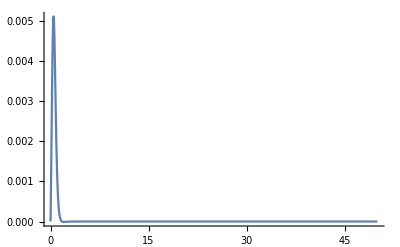

```mathematica
Plot[(rf1/.{θ->2}),{k3,0,50},PlotRange->All]
```

```mathematica
NIntegrate[nf1,{k3,2,∞},{θ,0,1},{y,-0.1,0.1}]
```

-5.4769×10^-7

```mathematica
NIntegrate[nf1,{k3,2,∞},{θ,1,2},{y,-0.1,0.1}]
NIntegrate[nf1,{k3,2,∞},{θ,2,π},{y,-0.1,0.1}]
NIntegrate[nf1,{k3,2,∞},{θ,π,4},{y,-0.1,0.1}]
NIntegrate[nf1,{k3,2,∞},{θ,4,5},{y,-0.1,0.1}]
NIntegrate[nf1,{k3,2,∞},{θ,5,2π},{y,-0.1,0.1}]
```

8.70302×10^-8

-0.0000110086

-0.000010971

1.2455×10^-7

-6.22809×10^-7

```mathematica
-0.0003502482925406578-0.00016918238480263378+0.0005308999910932711+0.00044424255381204345+2.785433873372089*^-6-0.0004355588986240081-5.476903301277313*^-7+8.703024576759769*^-8-0.000011008617445607892-0.000010971018154081132+1.2454973472767608*^-7-6.228089150216414*^-7
```

-1.52053×10^-10